```mathematica
Quit[]
```

```mathematica
ParallelEvaluate[Off[General::stop];];
```

```mathematica
A[r1_,r2_,r3_][ϕ1_,ϕ2_,ϕ3_]:=8 β^2 √(π/Nc)(NIntegrate[ϕ1[l/r1]ϕ2[l/r2] ϕ3[p/r3]/(p-(l-r2))^2,{p,0,r3},{l,0,r2}]-NIntegrate[ϕ1[l/r1]ϕ3[(l-r2)/r3] ϕ2[p/r2]/(p-l)^2,{p,0,r2},{l,r2,r1}])
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}],{n,0,20}];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=√(((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2)/(4 M1^2))
```

```mathematica
Atable=Range[1,18];
```

```mathematica
At[n_]:=Module[{ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3},
Table[
m2=m1;
{vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
{M1,ϕ1}={Mn[#][vals],ϕn[#][ϕ]}&[5];{M2,ϕ2}={Mn[#][vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][vals],ϕn[#][ϕ]}&[1];
ParallelTable[A[1, ω[M1,M2,M3],(1-ω[M1,M2,M3])][ϕ1,ϕ2,ϕ3],{ω,0.01,1,0.02}]
,{m1,0.5,1}]
]
```

```mathematica
At[5]
```

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.41-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.59
0 | 0.41).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.23-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.77
0 | 0.23).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.09-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.91
0 | 0.09).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.47-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.53
0 | 0.47).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.29-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.71
0 | 0.29).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.17-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.83
0 | 0.17).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.35-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.65
0 | 0.35).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.01-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.99
0 | 0.01).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.41
0.41 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.23
0.23 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.09
0.09 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.47
0.47 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.17
0.17 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.35
0.35 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.29
0.29 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.41-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.59
0 | 0.41).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.23-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.77
0 | 0.23).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.01
0.01 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.09-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.91
0 | 0.09).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.17-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.83
0 | 0.17).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.47-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.53
0 | 0.47).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.35-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.65
0 | 0.35).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.29-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.71
0 | 0.29).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.23
0.23 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.01-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.99
0 | 0.01).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.41
0.41 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.17
0.17 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.47
0.47 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.09
0.09 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.29
0.29 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.35
0.35 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.01
0.01 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.23-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.77
0 | 0.23).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.41-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.59
0 | 0.41).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.17-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.83
0 | 0.17).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.09-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.91
0 | 0.09).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.47-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.53
0 | 0.47).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.29-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.71
0 | 0.29).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.35-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.65
0 | 0.35).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.23
0.23 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.17
0.17 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.09
0.09 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.01-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.99
0 | 0.01).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.47
0.47 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.35
0.35 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.41
0.41 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.29
0.29 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.11-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.89
0 | 0.11).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.25-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.75
0 | 0.25).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.19-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.81
0 | 0.19).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.01
0.01 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.49-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.51
0 | 0.49).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.37-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.63
0 | 0.37).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.43-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.57
0 | 0.43).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.31-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.69
0 | 0.31).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.25
0.25 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.19
0.19 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.03-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.97
0 | 0.03).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.49
0.49 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.11
0.11 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.37
0.37 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.43
0.43 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.31
0.31 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.25-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.75
0 | 0.25).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.49-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.51
0 | 0.49).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.11-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.89
0 | 0.11).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.19-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.81
0 | 0.19).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.03
0.03 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.43-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.57
0 | 0.43).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.37-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.63
0 | 0.37).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.25
0.25 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.31-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.69
0 | 0.31).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.03-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.97
0 | 0.03).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.11
0.11 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.49
0.49 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.43
0.43 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.19
0.19 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.25-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.75
0 | 0.25).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.37
0.37 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.03
0.03 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.31
0.31 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.49-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.51
0 | 0.49).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.19-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.81
0 | 0.19).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.43-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.57
0 | 0.43).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.11-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.89
0 | 0.11).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.25
0.25 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.37-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.63
0 | 0.37).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.31-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.69
0 | 0.31).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.49
0.49 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.03-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.97
0 | 0.03).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.11
0.11 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.43
0.43 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.19
0.19 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.37
0.37 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.31
0.31 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.51-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.49
0 | 0.51).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.27-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.73
0 | 0.27).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.45-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.55
0 | 0.45).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.03
0.03 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.21-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.79
0 | 0.21).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.39-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.61
0 | 0.39).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.27
0.27 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.13-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.87
0 | 0.13).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.33-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.67
0 | 0.33).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.51
0.51 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.05-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.95
0 | 0.05).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.45
0.45 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.21
0.21 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.39
0.39 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.33
0.33 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.13
0.13 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.27-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.73
0 | 0.27).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.05
0.05 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.51-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.49
0 | 0.51).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.45-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.55
0 | 0.45).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.39-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.61
0 | 0.39).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.33-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.67
0 | 0.33).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.21-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.79
0 | 0.21).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.13-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.87
0 | 0.13).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(0.05-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.95
0 | 0.05).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.27
0.27 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.51
0.51 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.45
0.45 | 1).

NIntegrate::inumr: The integrand (2.46539 («19» √(1-(«1»)^2)+«56»+«450») «1» (8.00102×10^-16 √(1-Plus[«2»]^2)+0.147021 sin(2 cos^-1(-1+Times[«2»]))+5.92855×10^-15 sin(3 cos^-1(-1+Times[«2»]))+«57»+4.67208×10^-15 sin(49 cos^-1(-1+Times[«2»]))+0.00337545 sin(50 cos^-1(-1+Times[«2»]))+«450»))/(-l+p)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 0.33
0.33 | 1).

```mathematica
m1=0.5;
m2=m1;
{vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
```

```mathematica
{M1,ϕ1}={Mn[#][vals],ϕn[#][ϕ]}&[8];{M2,ϕ2}={Mn[#][vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][vals],ϕn[#][ϕ]}&[1];
```

```mathematica
ω[M1,M2,M3]
```

2.90916

```mathematica
A[1, ω[M1,M2,M3],(1-ω[M1,M2,M3])][ϕ1,ϕ2,ϕ3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,l} = {-0.000225074,2.9089358222325482348819165878683890014144708402454853057861328125}. NIntegrate obtained -2.62608-2.9902286729168893915581049377280359072183409559711471769780459672×10^487 ⅈ and 2.671194854308336357474525853320316326619412747669952726372744801×10^487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,l} = {2.905150247114720872369797444179084777715615928173065185546875,2.905150015150921740010592220215812631067819893360137939453125}. NIntegrate obtained 0.-8.6116085573127910318658752402228505850196637578789050374741194172×10^487 ⅈ and 2.9891899058276999153128203551229431164979451321541804114917787953×10^487 for the integral and error estimates.

-1.17753+2.520622790086×10^487 ⅈ

```mathematica
ParallelTable[A[1, ω,(1-ω)][ϕ1,ϕ2,ϕ3],{ω,0.01,1,0.02}]
```

```mathematica
ϕx=Determineϕx[m1,m2,β,Nx];
```

```mathematica
ϕ[x_]=Table[ϕx[[n+1]],{n,0,20}];
```

```mathematica
{M1,ϕ1}={Mn[#],ϕn[#]}&[5];{M2,ϕ2}={Mn[#],ϕn[#]}&[0];{M3,ϕ3}={Mn[#],ϕn[#]}&[1];
```

```mathematica
Atable=ParallelTable[A[1, ω,(1-ω)],{ω,0.01,1,0.02}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00895653 and 1.50035×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00867311 and 9.36724×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.017301 and 3.37514×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00962828 and 1.47355×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00427933 and 1.75951×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.011403 and 1.46529×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00669764 and 3.11103×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0149894 and 3.36744×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.032503 and 3.44876×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0105808 and 3.31647×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0133782 and 3.56896×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00858078 and 3.54728×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0159442 and 2.76947×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00409071 and 3.61802×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00936543 and 1.48888×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.019789 and 3.38469×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00341588 and 2.79802×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0256253 and 2.96392×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0241847 and 3.02287×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0097578 and 2.6988×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0227649 and 2.44317×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00627386 and 2.00166×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0199493 and 2.64829×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0153975 and 2.34456×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.015 and 1.87399×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00475215 and 2.055×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00430299 and 6.7358×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000554738 and 2.22243×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

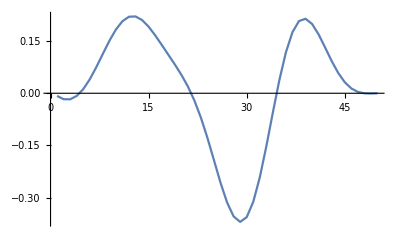

```mathematica
ListLinePlot[Re[Atable],PlotRange->All](*m=3.2*)
```

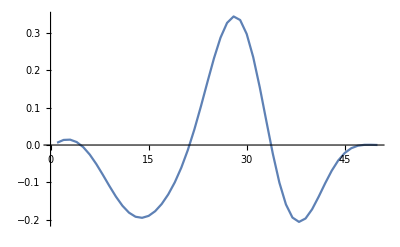

```mathematica
ListLinePlot[Re[Atable],PlotRange->All](*m=3.5*)
```

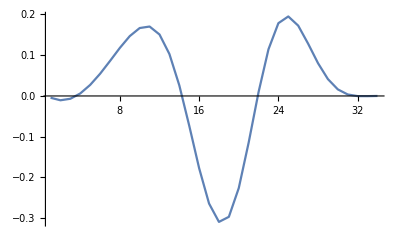

```mathematica
ListLinePlot[Re[Atable],PlotRange->All](*m=4*)
```

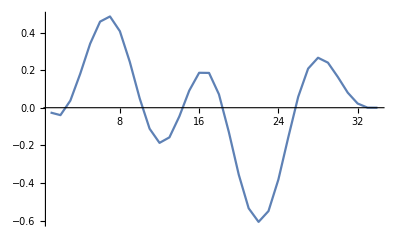

```mathematica
ListLinePlot[Re[Atable],PlotRange->All](*m=3*)
```